# < Harmonic oscillator from differential equation >

< Roshan Koirala >

## Final

```mathematica
Quit
```

Harmonic oscillators are very important problem in physics. They can explain from simple pendulum to the quantum fluctuation of vacuum. They are solution of differential equation. Most of the classical oscillator in the real life are not simple harmonic oscillator though. Various form of the frictional and dissipation force cause the damping of the oscillation. Damped oscillations are also solution of other set of differential equation. Finally, there can be external driving force acting on the top of the oscillating motion. Mathematically these are the solution of  Linear differential equation with inhomogeneous source term. We analyze the solution of the initial value problem of each of these differential equations in this essay.

### Analytical solution with no damping

The general solution of harmonic oscillator is the linear combination of sine and consine function. The boundary condition determines the value of the constant C_1 and C_2.

```mathematica
ϕ[x]/.DSolve[ϕ''[x]+ω^2 ϕ[x]==0,ϕ[x],x]⟦1⟧
```

C[1] Cos[x ω]+C[2] Sin[x ω]

### Numerical solution without damping

Throughout this notebook I keep the boundary conditions to be fixed: ϕ(0) = 0 and ϕ’’(0) = 1. The ω appearing in the differential equation has the interpretation of the frequency. In this part we will see how the change in ω affect the solution of the equation. The higher value of ω produce the larger number of waves in the given length. Amplitude of the wave depends on ω with A=1/ω.

```mathematica
solsSHM=Table[ϕ[x]/.NDSolve[{ϕ''[x]+ω^2 ϕ[x]==0, ϕ[0]==0,ϕ'[0]==1},ϕ[x],{x,0,10}],{ω,10}];
plotsSHM=Table[Plot[solsSHM⟦i⟧,{x,0,10},PlotStyle->Black,PlotRange->{-1,1},ImageSize->Large, AxesLabel->{Style["x", FontSize->20, Black],Style["ϕ[X]", FontSize->20, Black]}],{i,1,Length[solsSHM]}];
Manipulate[plotsSHM⟦i⟧,{i,1,Length[solsSHM],1, Appearance->"Open"}]
```

### Numerical solution with damping

In this section we introduce the damping term. Here, γ is called the damping coefficient. We see how the different value of γ affect the solution. Higher the value of γ, sooner the wave dies off. We have kept ω fixed for this purpose.

```mathematica
solsDamp=Table[ϕ[x]/.NDSolve[{ϕ''[x]+γ/10 ϕ'[x]+ω^2 ϕ[x]==0, ϕ[0]==0,ϕ'[0]==1}/.ω->10,ϕ[x],{x,0,10}],{γ,0,10}];
plotsDamp=Table[Plot[solsDamp⟦i⟧,{x,0,10},PlotStyle-> Black,PlotRange->{-0.1,0.1},ImageSize->Large, AxesLabel->{Style["x", FontSize->20, Black],Style["ϕ[X]", FontSize->20, Black]}],{i,1,Length[solsDamp]}];
Manipulate[plotsDamp⟦i⟧,{i,1,Length[solsDamp],1, Appearance->"Open"}]
```

### Forced oscillator

In this section I consider simple harmonic oscillator (no damping) with the sinusoidal source term. We see the effect of external source frequency f on the solution. The external source modulate the sinusoidal wave. However when the frequency of the oscillator ω is same as the frequency of the external source f the amplitude grows forever. This condition is called the resonance.

```mathematica
solsDrive=Table[ϕ[x]/.NDSolve[{ϕ''[x]+ ω^2 ϕ[x]==Sin[f x], ϕ[0]==0,ϕ'[0]==1}/.ω->10,ϕ[x],{x,0,10}],{f,0,10}];
plotsDrive=Table[Plot[solsDrive⟦i⟧,{x,0,10},PlotStyle->Black,PlotRange->{-0.11,0.11},ImageSize->Large,AxesLabel->{Style["x", FontSize->20, Black],Style["ϕ[X]", FontSize->20, Black]}],{i,1,Length[solsDrive]}];
Manipulate[plotsDrive⟦i⟧,{i,1,Length[solsDrive],1, Appearance->"Open"}]
```

### Resonance

Here, we consider the case ω = f as we discussed above. We can see the indefinite growth of the amplitude of the oscillation. In real practice this growth stops at some point where the energy of oscillation is capable to break the oscillating object.

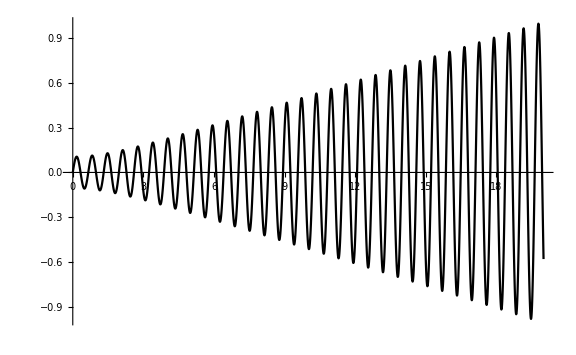

```mathematica
resonance=ϕ[x]/.NDSolve[{ϕ''[x]+ ω^2 ϕ[x]==Sin[f x], ϕ[0]==0,ϕ'[0]==1}/.{ω->10,f->10},ϕ[x],{x,0,20}];
Plot[resonance,{x,0,20}, PlotStyle->Black, ImageSize->Large]
```